```mathematica
DifferentialD[Cos[Log[x]]]
```

ⅆCos[Log[x]]

```mathematica
f[x_] = Cos[Log[x]]
```

Cos[Log[x]]

```mathematica
f'[x]
f''[x]
```

-Sin[Log[x]]/x

-Cos[Log[x]]/x^2+Sin[Log[x]]/x^2

```mathematica
g[x_] = Sin[Log[x]]
x^2*g''[x] + x*g'[x] + g[x]
```

Sin[Log[x]]

Cos[Log[x]]+Sin[Log[x]]+x^2 (-Cos[Log[x]]/x^2-Sin[Log[x]]/x^2)

```mathematica
Simplify[%]
```

0

```mathematica
DSolve[{y'[x]==xy[x],y[0]==2},y[x],x]
```

DSolve::deqn: Equation or list of equations expected instead of True in the first argument {True,True}.

DSolve[{True,True},y[x],x]

```mathematica
DSolve[y'[z]==zy[z],y[z],z]
```

DSolve::deqn: Equation or list of equations expected instead of True in the first argument True.

DSolve[True,y[z],z]

```mathematica
DSolve[y'[x]==y[x] + a Sin[x],y[x],x]
```

{{y[x]→-a Sin[x]+xy[x]}}

```mathematica
Clear[Global,"*"]
```

Clear::wrsym: Symbol a is Protected.

Clear::wrsym: Symbol b is Protected.

Clear::wrsym: Symbol c is Protected.

General::stop: Further output of Clear::wrsym will be suppressed during this calculation.

Clear::spsym: Special symbol $ActivationGroupID cannot be cleared.

Clear::spsym: Special symbol $ActivationKey cannot be cleared.

Clear::spsym: Special symbol $ActivationUserRegistered cannot be cleared.

General::stop: Further output of Clear::spsym will be suppressed during this calculation.

```mathematica
Clear["Global`*"]
```

```mathematica
DSolve[y'[x]==y[x] + a Sin[x],y[x],x]
```

{{y[x]→ⅇ^x C[1]-1/2 a (Cos[x]+Sin[x])}}

```mathematica
PacletInstall@"path/to/downloaded/CellsToTeX-0.2.2.paclet"
```

$Failed

```mathematica
PacletInstall@"http://github.com/jkuczm/MathematicaCellsToTeX/releases/download/v0.2.2/CellsToTeX-0.2.2.paclet"
```

$Failed

```mathematica
PacletInstall"http://github.com/jkuczm/MathematicaCellsToTeX/releases/download/v0.2.2/CellsToTeX-0.2.2.paclet"
```

http://github.com/jkuczm/MathematicaCellsToTeX/releases/download/v0.2.2/CellsToTeX-0.2.2.paclet PacletInstall

```mathematica
Import["https://raw.githubusercontent.com/jkuczm/MathematicaCellsToTeX/master/NoInstall.m"]
```

$Failed

```mathematica
<<https://paclets.github.io/PacletServer/Install.wl
PublicPacletInstall["CellsToTeX"]
```

Failure[…]

```mathematica
Import@"https://raw.githubusercontent.com/jkuczm/MathematicaCellsToTeX/master/NoInstall.m"
```

$Failed

{{y[x]→1/4 ⅇ^x (-1+2 x)+ⅇ^x C[1]+ⅇ^-x C[2]}}

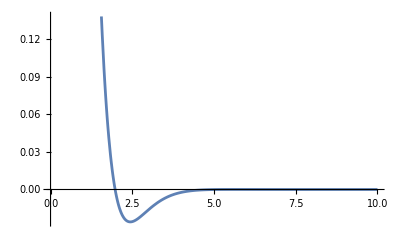
$DisplayFunction[-Graphics-]

```mathematica
y
```

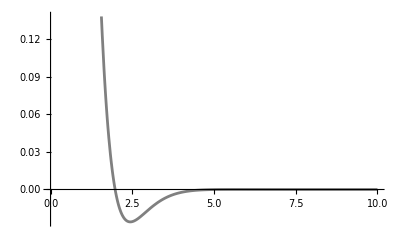
$DisplayFunction[-Graphics-]

```mathematica
Plot[Exp[-2x]*(3Sin[x] + 7Cos[x]),{x,0,10},PlotStyle->Gray]
```

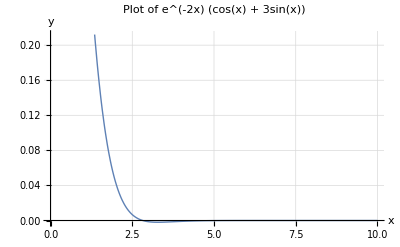
$DisplayFunction[-Graphics-]

```mathematica
Plot[Exp[-2 x] (Cos[x]+3 Sin[x]),{x,0,10},PlotStyle->Thick,AxesLabel->{"x","y"},PlotLabel->"Plot of e^(-2x) (cos(x) + 3sin(x))",GridLines->Automatic]
```

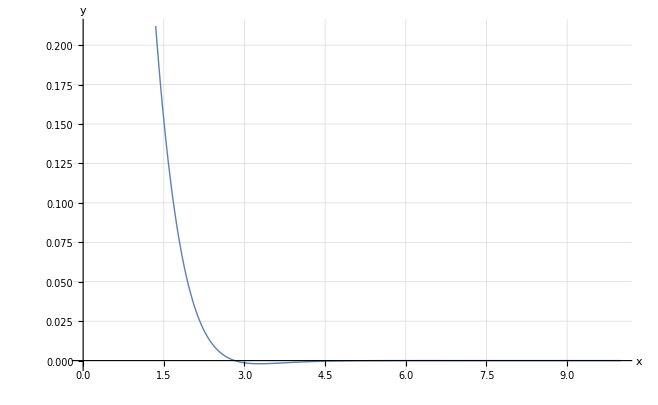

```mathematica
$DisplayFunction=Identity;
Plot[Exp[-2 x] (Cos[x]+3 Sin[x]),{x,0,10},PlotStyle->Thick,AxesLabel->{"x","y"},GridLines->Automatic]
```

```mathematica
Clear[x,y]
```

```mathematica
DSolve[y'[x]^2 +y[x] == 2,y,x]
```

{{y→Function[{x},1/4 (8-x^2-2 x C[1]-C[1]^2)]},{y→Function[{x},1/4 (8-x^2+2 x C[1]-C[1]^2)]}}

```mathematica
Simplify[%]
```

{{y→Function[{x},1/4 (8-x^2-2 x C[1]-C[1]^2)]},{y→Function[{x},1/4 (8-x^2+2 x C[1]-C[1]^2)]}}

```mathematica
DSolve[y''[x]*y'''[x] == 0,y,x]
```

{{y→Function[{x},C[1]+x C[2]]},{y→Function[{x},C[1]+x C[2]+x^2 C[3]]}}

```mathematica
DSolve[y'[x]-y[x]^2 == 1,y,x]
```

{{y→Function[{x},Tan[x+C[1]]]}}

```mathematica
DSolve[y''''[x]==x,y,x]
```

{{y→Function[{x},x^5/120+C[1]+x C[2]+x^2 C[3]+x^3 C[4]]}}

```mathematica
DSolve[y''''[x]-y[x] == x^3,y,x]
```

{{y→Function[{x},-x^3+ⅇ^x C[1]+ⅇ^-x C[3]+C[2] Cos[x]+C[4] Sin[x]]}}

```mathematica
Solve[r*(r-1)^2(r-4) + 1 == 0,r]
```

{{r→Root1.52Root[1-4 #1+9 #1^2-6 #1^3+#1^4&,1]1.5153596067063246},{r→Root3.97Root[1-4 #1+9 #1^2-6 #1^3+#1^4&,2]3.971483205255795},{r→Root0.257-0.317 ⅈRoot[1-4 #1+9 #1^2-6 #1^3+#1^4&,3]0.25657859401894034},{r→Root0.257+0.317 ⅈRoot[1-4 #1+9 #1^2-6 #1^3+#1^4&,4]0.25657859401894034}}

```mathematica
Roots[x*(x-1)^2*(x-4) + 1==0,x]
```

x==3/2-1/2 √(3+1/3 (135-6 √249)^(1/3)+(45+2 √249)^(1/3)/3^(2/3))-1/2 √(6-1/3 (135-6 √249)^(1/3)-(45+2 √249)^(1/3)/3^(2/3)-8/(√(3+1/3 (135-6 √249)^(1/3)+(45+2 √249)^(1/3)/3^(2/3))))||x==3/2-1/2 √(3+1/3 (135-6 √249)^(1/3)+(45+2 √249)^(1/3)/3^(2/3))+1/2 √(6-1/3 (135-6 √249)^(1/3)-(45+2 √249)^(1/3)/3^(2/3)-8/(√(3+1/3 (135-6 √249)^(1/3)+(45+2 √249)^(1/3)/3^(2/3))))||x==3/2+1/2 √(3+1/3 (135-6 √249)^(1/3)+(45+2 √249)^(1/3)/3^(2/3))-1/2 √(6-1/3 (135-6 √249)^(1/3)-(45+2 √249)^(1/3)/3^(2/3)+8/(√(3+1/3 (135-6 √249)^(1/3)+(45+2 √249)^(1/3)/3^(2/3))))||x==3/2+1/2 √(3+1/3 (135-6 √249)^(1/3)+(45+2 √249)^(1/3)/3^(2/3))+1/2 √(6-1/3 (135-6 √249)^(1/3)-(45+2 √249)^(1/3)/3^(2/3)+8/(√(3+1/3 (135-6 √249)^(1/3)+(45+2 √249)^(1/3)/3^(2/3))))

```mathematica
TeXForm[%]
```

x=\frac{3}{2}-\frac{1}{2} \sqrt{3+\frac{1}{3} \sqrt[3]{135-6 \sqrt{249}}+\frac{\sqrt[3]{45+2
   \sqrt{249}}}{3^{2/3}}}-\frac{1}{2} \sqrt{6-\frac{1}{3} \sqrt[3]{135-6 \sqrt{249}}-\frac{\sqrt[3]{45+2
   \sqrt{249}}}{3^{2/3}}-\frac{8}{\sqrt{3+\frac{1}{3} \sqrt[3]{135-6 \sqrt{249}}+\frac{\sqrt[3]{45+2
   \sqrt{249}}}{3^{2/3}}}}}\lor x=\frac{3}{2}-\frac{1}{2} \sqrt{3+\frac{1}{3} \sqrt[3]{135-6
   \sqrt{249}}+\frac{\sqrt[3]{45+2 \sqrt{249}}}{3^{2/3}}}+\frac{1}{2} \sqrt{6-\frac{1}{3} \sqrt[3]{135-6
   \sqrt{249}}-\frac{\sqrt[3]{45+2 \sqrt{249}}}{3^{2/3}}-\frac{8}{\sqrt{3+\frac{1}{3} \sqrt[3]{135-6
   \sqrt{249}}+\frac{\sqrt[3]{45+2 \sqrt{249}}}{3^{2/3}}}}}\lor x=\frac{3}{2}+\frac{1}{2} \sqrt{3+\frac{1}{3}
   \sqrt[3]{135-6 \sqrt{249}}+\frac{\sqrt[3]{45+2 \sqrt{249}}}{3^{2/3}}}-\frac{1}{2} \sqrt{6-\frac{1}{3}
   \sqrt[3]{135-6 \sqrt{249}}-\frac{\sqrt[3]{45+2 \sqrt{249}}}{3^{2/3}}+\frac{8}{\sqrt{3+\frac{1}{3}
   \sqrt[3]{135-6 \sqrt{249}}+\frac{\sqrt[3]{45+2 \sqrt{249}}}{3^{2/3}}}}}\lor x=\frac{3}{2}+\frac{1}{2}
   \sqrt{3+\frac{1}{3} \sqrt[3]{135-6 \sqrt{249}}+\frac{\sqrt[3]{45+2 \sqrt{249}}}{3^{2/3}}}+\frac{1}{2}
   \sqrt{6-\frac{1}{3} \sqrt[3]{135-6 \sqrt{249}}-\frac{\sqrt[3]{45+2
   \sqrt{249}}}{3^{2/3}}+\frac{8}{\sqrt{3+\frac{1}{3} \sqrt[3]{135-6 \sqrt{249}}+\frac{\sqrt[3]{45+2
   \sqrt{249}}}{3^{2/3}}}}}

```mathematica
TeXForm[x==3/2-1/2 √(3+1/3 (135-6 √249)^(1/3)+(45+2 √249)^(1/3)/3^(2/3))-1/2 √(6-1/3 (135-6 √249)^(1/3)-(45+2 √249)^(1/3)/3^(2/3)-8/(√(3+1/3 (135-6 √249)^(1/3)+(45+2 √249)^(1/3)/3^(2/3))))]
```

x=\frac{3}{2}-\frac{1}{2} \sqrt{3+\frac{1}{3} \sqrt[3]{135-6 \sqrt{249}}+\frac{\sqrt[3]{45+2
   \sqrt{249}}}{3^{2/3}}}-\frac{1}{2} \sqrt{6-\frac{1}{3} \sqrt[3]{135-6 \sqrt{249}}-\frac{\sqrt[3]{45+2
   \sqrt{249}}}{3^{2/3}}-\frac{8}{\sqrt{3+\frac{1}{3} \sqrt[3]{135-6 \sqrt{249}}+\frac{\sqrt[3]{45+2
   \sqrt{249}}}{3^{2/3}}}}}

```mathematica
TeXForm[x==3/2-1/2 √(3+1/3 (135-6 √249)^(1/3)+(45+2 √249)^(1/3)/3^(2/3))+1/2 √(6-1/3 (135-6 √249)^(1/3)-(45+2 √249)^(1/3)/3^(2/3)-8/(√(3+1/3 (135-6 √249)^(1/3)+(45+2 √249)^(1/3)/3^(2/3))))]
```

x=\frac{3}{2}-\frac{1}{2} \sqrt{3+\frac{1}{3} \sqrt[3]{135-6 \sqrt{249}}+\frac{\sqrt[3]{45+2
   \sqrt{249}}}{3^{2/3}}}+\frac{1}{2} \sqrt{6-\frac{1}{3} \sqrt[3]{135-6 \sqrt{249}}-\frac{\sqrt[3]{45+2
   \sqrt{249}}}{3^{2/3}}-\frac{8}{\sqrt{3+\frac{1}{3} \sqrt[3]{135-6 \sqrt{249}}+\frac{\sqrt[3]{45+2
   \sqrt{249}}}{3^{2/3}}}}}

```mathematica
TeXForm[x==3/2+1/2 √(3+1/3 (135-6 √249)^(1/3)+(45+2 √249)^(1/3)/3^(2/3))-1/2 √(6-1/3 (135-6 √249)^(1/3)-(45+2 √249)^(1/3)/3^(2/3)+8/(√(3+1/3 (135-6 √249)^(1/3)+(45+2 √249)^(1/3)/3^(2/3))))]
```

x=\frac{3}{2}+\frac{1}{2} \sqrt{3+\frac{1}{3} \sqrt[3]{135-6 \sqrt{249}}+\frac{\sqrt[3]{45+2
   \sqrt{249}}}{3^{2/3}}}-\frac{1}{2} \sqrt{6-\frac{1}{3} \sqrt[3]{135-6 \sqrt{249}}-\frac{\sqrt[3]{45+2
   \sqrt{249}}}{3^{2/3}}+\frac{8}{\sqrt{3+\frac{1}{3} \sqrt[3]{135-6 \sqrt{249}}+\frac{\sqrt[3]{45+2
   \sqrt{249}}}{3^{2/3}}}}}

```mathematica
TeXForm[x==3/2+1/2 √(3+1/3 (135-6 √249)^(1/3)+(45+2 √249)^(1/3)/3^(2/3))+1/2 √(6-1/3 (135-6 √249)^(1/3)-(45+2 √249)^(1/3)/3^(2/3)+8/(√(3+1/3 (135-6 √249)^(1/3)+(45+2 √249)^(1/3)/3^(2/3))))]
```

x=\frac{3}{2}+\frac{1}{2} \sqrt{3+\frac{1}{3} \sqrt[3]{135-6 \sqrt{249}}+\frac{\sqrt[3]{45+2
   \sqrt{249}}}{3^{2/3}}}+\frac{1}{2} \sqrt{6-\frac{1}{3} \sqrt[3]{135-6 \sqrt{249}}-\frac{\sqrt[3]{45+2
   \sqrt{249}}}{3^{2/3}}+\frac{8}{\sqrt{3+\frac{1}{3} \sqrt[3]{135-6 \sqrt{249}}+\frac{\sqrt[3]{45+2
   \sqrt{249}}}{3^{2/3}}}}}

```mathematica
TeXForm[x==3/2+1/2 √(3+1/3 (135-6 √249)^(1/3)+(45+2 √249)^(1/3)/3^(2/3))+1/2 √(6-1/3 (135-6 √249)^(1/3)-(45+2 √249)^(1/3)/3^(2/3)+8/(√(3+1/3 (135-6 √249)^(1/3)+(45+2 √249)^(1/3)/3^(2/3))))]
```

x=\frac{3}{2}+\frac{1}{2} \sqrt{3+\frac{1}{3} \sqrt[3]{135-6 \sqrt{249}}+\frac{\sqrt[3]{45+2
   \sqrt{249}}}{3^{2/3}}}+\frac{1}{2} \sqrt{6-\frac{1}{3} \sqrt[3]{135-6 \sqrt{249}}-\frac{\sqrt[3]{45+2
   \sqrt{249}}}{3^{2/3}}+\frac{8}{\sqrt{3+\frac{1}{3} \sqrt[3]{135-6 \sqrt{249}}+\frac{\sqrt[3]{45+2
   \sqrt{249}}}{3^{2/3}}}}}

```mathematica
JordanDecomposition[{{4,2,1},{0,4,2},{0,0,4}}]
```

{{{1,0,0},{0,1/2,-1/8},{0,0,1/4}},{{4,1,0},{0,4,1},{0,0,4}}}

```mathematica
MatrixForm[%]
```

((1
0
0) | (0
1/2
-1/8) | (0
0
1/4)
(4
1
0) | (0
4
1) | (0
0
4))

```mathematica
JordanDecomposition[{{4,0,0},{2,4,0},{1,2,4}}]
MatrixForm[%]
```

{{{0,0,1/4},{0,1/2,-1/8},{1,0,0}},{{4,1,0},{0,4,1},{0,0,4}}}

((0
0
1/4) | (0
1/2
-1/8) | (1
0
0)
(4
1
0) | (0
4
1) | (0
0
4))

```mathematica
Roots[(2-x)^3*(1-x)*(-1-x) + 10 == 0,x]
```

x==Root-0.702Root[-2-12 #1-2 #1^2+11 #1^3-6 #1^4+#1^5&,1]-0.7023216420195433||x==Root-0.178Root[-2-12 #1-2 #1^2+11 #1^3-6 #1^4+#1^5&,2]-0.1775653289792452||x==Root3.06Root[-2-12 #1-2 #1^2+11 #1^3-6 #1^4+#1^5&,3]3.061092435840131||x==Root1.91-1.26 ⅈRoot[-2-12 #1-2 #1^2+11 #1^3-6 #1^4+#1^5&,4]1.9093972675793283||x==Root1.91+1.26 ⅈRoot[-2-12 #1-2 #1^2+11 #1^3-6 #1^4+#1^5&,5]1.9093972675793283

```mathematica
TeXForm[%]
```

x=\text{Root}\left[\text{$\#$1}^5-6 \text{$\#$1}^4+11 \text{$\#$1}^3-2 \text{$\#$1}^2-12
   \text{$\#$1}-2\&,1\right]\lor x=\text{Root}\left[\text{$\#$1}^5-6 \text{$\#$1}^4+11 \text{$\#$1}^3-2
   \text{$\#$1}^2-12 \text{$\#$1}-2\&,2\right]\lor x=\text{Root}\left[\text{$\#$1}^5-6 \text{$\#$1}^4+11
   \text{$\#$1}^3-2 \text{$\#$1}^2-12 \text{$\#$1}-2\&,3\right]\lor x=\text{Root}\left[\text{$\#$1}^5-6
   \text{$\#$1}^4+11 \text{$\#$1}^3-2 \text{$\#$1}^2-12 \text{$\#$1}-2\&,4\right]\lor
   x=\text{Root}\left[\text{$\#$1}^5-6 \text{$\#$1}^4+11 \text{$\#$1}^3-2 \text{$\#$1}^2-12
   \text{$\#$1}-2\&,5\right]

```mathematica
Roots[(2-x)^3*(1-x)*(-1-x) + 10 == 0,x]
```

x==Root-0.702Root[-2-12 #1-2 #1^2+11 #1^3-6 #1^4+#1^5&,1]-0.7023216420195433||x==Root-0.178Root[-2-12 #1-2 #1^2+11 #1^3-6 #1^4+#1^5&,2]-0.1775653289792452||x==Root3.06Root[-2-12 #1-2 #1^2+11 #1^3-6 #1^4+#1^5&,3]3.061092435840131||x==Root1.91-1.26 ⅈRoot[-2-12 #1-2 #1^2+11 #1^3-6 #1^4+#1^5&,4]1.9093972675793283||x==Root1.91+1.26 ⅈRoot[-2-12 #1-2 #1^2+11 #1^3-6 #1^4+#1^5&,5]1.9093972675793283

```mathematica
Simplify[(x)*(x-1)*(x-2)*(x-3) + 6*x*(x-1)*(x-2) + 9*x*(x-1) + 3*x + 1]
```

(1+x^2)^2

```mathematica
JordanDecomposition[{{27,48,81},{-6,0,0},{1,0,3}}]
```

{{{3,18,2},{-3,-9,-1/4},{1,2,0}},{{6,0,0},{0,12,1},{0,0,12}}}

```mathematica
Map[MatrixForm,%]
```

{(3 | 18 | 2
-3 | -9 | -1/4
1 | 2 | 0),(6 | 0 | 0
0 | 12 | 1
0 | 0 | 12)}

```mathematica
{{6,0,0},{0,12,1},{0,0,12}}.{{6,0,0},{0,12,1},{0,0,12}}
```

{{36,0,0},{0,144,24},{0,0,144}}

```mathematica
Det[{{1,Exp[-4*t],2*Exp[3*t]},{6,2*Exp[-4*t],3*Exp[3*t]},{-13,-Exp[-4*t],2*Exp[3*t]}}]
```

-4 ⅇ^-t

```mathematica
A = {{1,0,2,-1.8,0},{0,5.1,0,-1,3},{1,2,-3,0,0},{0,1,-3.1,4,0},{-2.8,0,0,1.5,1}}
MatrixForm[Eigenvalues[A]]
MatrixForm[Eigenvectors[A]]
```

{{1,0,2,-1.8,0},{0,5.1,0,-1,3},{1,2,-3,0,0},{0,1,-3.1,4,0},{-2.8,0,0,1.5,1}}

(5.05452
4.09561
-2.92362
2.02882
-0.155338)

(-0.0312209 | -0.949058 | -0.239535 | -0.195825 | -0.0508861
-0.280232 | -0.836611 | -0.275304 | 0.176045 | 0.338775
0.262219 | -0.162664 | -0.826218 | -0.346439 | 0.31957
-0.313235 | -0.64181 | -0.31754 | -0.173787 | 0.599108
-0.301294 | 0.466599 | 0.222136 | 0.0534311 | -0.799567)

```mathematica
{eigenvaluesA, eigenvectorsA}=Eigensystem[A]
```

{{5.05452,4.09561,-2.92362,2.02882,-0.155338},{{-0.0312209,-0.949058,-0.239535,-0.195825,-0.0508861},{-0.280232,-0.836611,-0.275304,0.176045,0.338775},{0.262219,-0.162664,-0.826218,-0.346439,0.31957},{-0.313235,-0.64181,-0.31754,-0.173787,0.599108},{-0.301294,0.466599,0.222136,0.0534311,-0.799567}}}

```mathematica
MatrixForm[eigenvectorsA]
MatrixForm[eigenvaluesA]
```

(-0.0312209 | -0.949058 | -0.239535 | -0.195825 | -0.0508861
-0.280232 | -0.836611 | -0.275304 | 0.176045 | 0.338775
0.262219 | -0.162664 | -0.826218 | -0.346439 | 0.31957
-0.313235 | -0.64181 | -0.31754 | -0.173787 | 0.599108
-0.301294 | 0.466599 | 0.222136 | 0.0534311 | -0.799567)

(5.05452
4.09561
-2.92362
2.02882
-0.155338)

```mathematica
eigenvectorsA[[5]]
```

{-0.301294,0.466599,0.222136,0.0534311,-0.799567}

```mathematica
B = {{3,2,4},{2,0,2},{4,2,3}};
CharacteristicPolynomial[B,x]
Roots[0==-CharacteristicPolynomial[B,x],x]
```

8+15 x+6 x^2-x^3

x==-1||x==-1||x==8

Roots[Roots[8+15 x+6 x^2-x^3],x]

```mathematica
JordanDecomposition[{{3,2,4},{2,0,2},{4,2,3}}]
```

{{{-1,-1,2},{0,2,1},{1,0,2}},{{-1,0,0},{0,-1,0},{0,0,8}}}

```mathematica
MatrixForm[%]
```

((-1
-1
2) | (0
2
1) | (1
0
2)
(-1
0
0) | (0
-1
0) | (0
0
8))

```mathematica
CharacteristicPolynomial[{{2,1,2},{3,0,6},{-4,0,-3}},x]
```

-15+x-x^2-x^3

```mathematica
Roots[%==0,x]
```

x==1-2 ⅈ||x==1+2 ⅈ||x==-3

```mathematica
Simplify[%]
```

x==1/3 (5-4/(-71+3 √561)^(1/3)+2 (-71+3 √561)^(1/3))||x==1/3 (5+(2+2 ⅈ √3)/(-71+3 √561)^(1/3)+ⅈ (ⅈ+√3) (-71+3 √561)^(1/3))||x==1/3 (5+(2-2 ⅈ √3)/(-71+3 √561)^(1/3)+(-1-ⅈ √3) (-71+3 √561)^(1/3))

```mathematica
Integrate[Exp[I*k*x]/(x-a),{x,-Infinity,Infinity},PrincipalValue->True]
```

ConditionalExpression[-π MeijerG[{{0},{-1/2}},{{0,0},{-1/2}},-ⅈ a k]+π^(3/2) MeijerG[{{0},{-1/4,1/4}},{{0,0,1/2},{-1/4,1/4}},(a^2 k^2)/4]+1/2 ⅈ Sign[k] (2 CosIntegral[-a Abs[k]] Sin[a Abs[k]]+Cos[a Abs[k]] (π-2 SinIntegral[a Abs[k]])), k∈ℝ&&Re[a]<0&&Im[a]==0]

```mathematica
Apart[(z)/((z^2 - 1)*(z-I)^2*(z+I)^2),z]
```

1/(8 (-1+z))+ⅈ/(8 (-ⅈ+z)^2)-1/(8 (-ⅈ+z))-ⅈ/(8 (ⅈ+z)^2)-1/(8 (ⅈ+z))+1/(8 (1+z))

```mathematica
Simplify[%]
```

z/((-1+z^2) (1+z^2)^2)

```mathematica
Integrate[x/(1 + x^4),{x,0,Infinity}]
```

π/4

```mathematica
Eigensystem[{{1,-4},{2,5}}]
```

{{3+2 ⅈ,3-2 ⅈ},{{-1+ⅈ,1},{-1-ⅈ,1}}}

```mathematica
Eigensystem[{{5,2},{-4,1}}]
```

{{3+2 ⅈ,3-2 ⅈ},{{-1-ⅈ,2},{-1+ⅈ,2}}}